```mathematica
L = 1;
F[x_]:= {Piecewise[{{x,0<x<L/2},{1-x,L/2<x<L}}]}
F1[x_]:= {Piecewise[{{x,-L/2<x<0},{-1-x,-L<x<-L/2}}]}
F2[x_]:=If [x>0,F[x],F1[x]];
Range[F2[x]]={-L,L};

B[n_]=Simplify[2/L ∫_0^L F2[x]*Sin[n*Pi*x/L]ⅆx,Assumptions-> n∈Integers]
```

Set::write: Tag Range in Range[If[x>0,F[x],F1[x]]] is Protected.

{(4 Sin[(n π)/2])/(n^2 π^2)}

{0,1}

{-1,0}

{1,2}

{2,3}

{-2,-1}

{-3,-2}

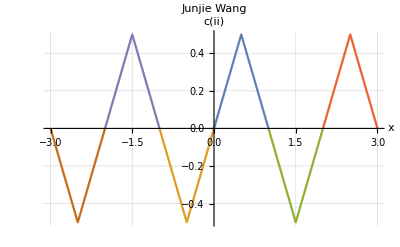

```mathematica
L = 1;
Fo[x_]:= {Piecewise[{{x,0<x<L/2},{1-x,L/2<x<L}}]}
F[x_]:=If[0<x<L,Fo[x],Null]
Range[F[x]]={0,L}
F1o[x_]:= {Piecewise[{{x,-L/2<x<0},{-1-x,-L<x<-L/2}}]}
F1[x_]:=If[-L<x<0,F1o[x],Null]
Range[F1[x]]={-L,0}
F2o[x_]:= {Piecewise[{{x-2,3L/2<x<2L},{1-x,L<x<3L/2}}]}
F2[x_]:=If[L<x<2L,F2o[x],Null]
Range[F2[x]]={L,2L}
F3o[x_]:= {Piecewise[{{x-2,2L<x<5L/2},{3-x,5L/2<x<3L}}]}
F3[x_]:=If[2L<x<3L,F3o[x],Null]
Range[F3[x]]={2L,3L}
F4o[x_]:= {Piecewise[{{x+2,-2L<x<-3L/2},{-1-x,-3L/2<x<-L}}]}
F4[x_]:=If[-2L<x<-L,F4o[x],Null]
Range[F4[x]]={-2L,-L}
F5o[x_]:= {Piecewise[{{x+2,-5L/2<x<-2L},{-1-(x+2),-3L<x<-5L/2}}]}
F5[x_]:=If[-3L<x<-2L,F5o[x],Null]
Range[F2[x]]={-3L,-2L}
Plot[{F[x],F1[x],F2[x],F3[x],F4[x],F5[x]},{x,-3L,3L},
AxesLabel-> {"x","c(ii)"},
PlotLabel->"Junjie Wang",
GridLines->Automatic,
BaseStyle->{FontSize-> 18}]
```

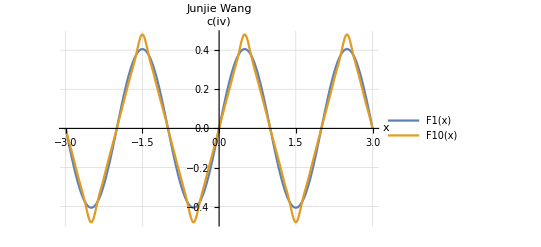

```mathematica
F1[x_]:={Sum[(4 Sin[(n π)/2])/(n^2 π^2)*Sin[n*Pi*x],{n,1,1}]}
F10[x_]:={Sum[(4 Sin[(n π)/2])/(n^2 π^2)*Sin[n*Pi*x],{n,1,10}]}
Plot[{F1[x],F10[x]},{x,-3,3},

AxesLabel-> {"x","c(iv)"},
PlotLabel->"Junjie Wang",
PlotLegends->"Expressions",
GridLines->Automatic,
BaseStyle->{FontSize-> 18}]
```